-Sono al caso α= 0

Ecco Q:   1

-Sono al caso α= 0.02

Ecco Q:   50

-Sono al caso α= 0.04

Ecco Q:   25

-Sono al caso α= 0.06

Ecco Q:   50

-Sono al caso α= 0.08

Ecco Q:   25

-Sono al caso α= 0.1

Ecco Q:   10

-Sono al caso α= 0.12

Ecco Q:   25

-Sono al caso α= 0.14

Ecco Q:   50

-Sono al caso α= 0.16

Ecco Q:   25

-Sono al caso α= 0.18

Ecco Q:   50

-Sono al caso α= 0.2

Ecco Q:   5

-Sono al caso α= 0.22

Ecco Q:   50

-Sono al caso α= 0.24

Ecco Q:   25

-Sono al caso α= 0.26

Ecco Q:   50

-Sono al caso α= 0.28

Ecco Q:   25

-Sono al caso α= 0.3

Ecco Q:   10

-Sono al caso α= 0.32

Ecco Q:   25

-Sono al caso α= 0.34

Ecco Q:   50

-Sono al caso α= 0.36

Ecco Q:   25

-Sono al caso α= 0.38

Ecco Q:   50

-Sono al caso α= 0.4

Ecco Q:   5

-Sono al caso α= 0.42

Ecco Q:   50

-Sono al caso α= 0.44

Ecco Q:   25

-Sono al caso α= 0.46

Ecco Q:   50

-Sono al caso α= 0.48

Ecco Q:   25

-Sono al caso α= 0.5

Ecco Q:   2

3.8763

-3.8763

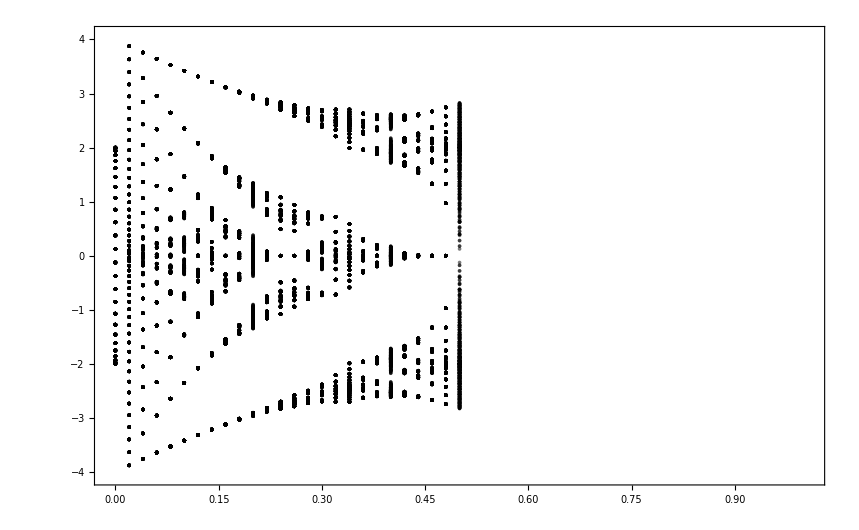

```mathematica
Begin["Pr1`"];
ClearAll["Pr1`*"];
Clear[v, w, R, r, Ncells, Nn];

t=1.
Ncellsy=50;
Ncellsx=50;
αlist={0,0.01, 0.02, 0.03, 0.04, 0.05, 0.06, 0.07, 0.08,0.09,  0.1,0.11,  0.12, 0.13, 0.14, 0.15, 0.16, 0.17, 0.18, 0.19, 0.2, 0.21, 0.22, 0.23, 0.24, 0.25, 0.26,0.27, 0.28, 0.29, 0.3, 0.31, 0.32, 0.33, 0.34, 0.35, 0.36,0.37,  0.38,0.39,  0.4, 0.41, 0.42,0.43,  0.44,0.45, 0.46, 0.47, 0.48, 0.49, 0.5}; 
Qlist={};
En={};


For[kk=1, kk<Length[αlist]+1, kk++,
α=αlist[[kk]];
Q=If[α>0,Denominator[Rationalize[α]], 1];
Print["-Sono al caso α= " , α];
Print["Ecco Q:   " , Q];
Qlist=Append[Qlist, Q];
If[Q>2,   MM=With[{Nn=N[Q], pattern={t,t}},SparseArray[{Band[{1,2},{-2,-1}]->pattern,Band[{2,1},{-1,-2}]->pattern},{Nn,Nn}]],   
If[Q==2, MM=SparseArray[{{1,2}->t,{2,1}->t}], MM={{0}}   ] ]    ;
MM=Normal[MM];
Enα={};
NNN=IntegerPart[Ncellsy/Q];
For[m=0, m<NNN, m++,  ky=2*π/Ncellsy*m;
For[n=0,  n<Ncellsx, n++, kx=2*π/(Q*Ncellsx)*n; 
Matrix=Table[MM[[i]][[j]],{i,Q},{j,Q}];
Matrix[[1,Q]]=Matrix[[1,Q]]+t*N[ⅇ^(-ⅈ*Q*kx)];
Matrix[[Q,1]]=Matrix[[Q,1]]+t*N[ⅇ^(+ⅈ*Q*kx)];
For[q=1, q<Q+1, q++,  Matrix[[q,q]]=2*t*N[Cos[ky-2*π*α*q]] ];
(* Print[MatrixForm[Matrix]];  *)

If[ Q>1,   Enα=Append[Enα, Eigenvalues[Matrix]], Enα=Append[Enα, {Matrix[[1,1]]}]  ];

];
];

En=Append[En, Enα];
]
En  ;

(*
Maxx=Max[En]
Minn=Min[En]






Enb={};
For[kk=1, kk<Length[αlist]+1, kk++,
   Enbα={};
NNN=IntegerPart[Ncellsy/Qlist[[kk]]];
For[m=1,m<NNN+1, m++,
For[n=1,n<Ncellsx+1, n++,
For[q=1,q<Qlist[[kk]]+1, q++,
Enbα=Append[Enbα,  { αlist[[kk]] ,En[[kk]][[(m-1) *Ncellsx+n]][[q]]   } ];
];
];
];
Enb=Append[Enb,  Enbα ];
]; *)


Enc={};
For[kk=1, kk<Length[αlist]+1, kk++,
NNN=IntegerPart[Ncellsy/Qlist[[kk]]];
For[m=1,m<NNN+1, m++,
For[n=1,n<Ncellsx+1, n++,
For[q=1,q<Qlist[[kk]]+1, q++,
Enc=Append[Enc,  { αlist[[kk]] ,En[[kk]][[(m-1) *Ncellsx+n]][[q]]   } ];
];
];
];
];



Show[
ListPlot[Enc, PlotRange->{{-0.01, 1.01},{Minn-0.2, Maxx+0.2}}, Axes->False, PlotStyle->{Black, Opacity[0.3], PointSize[.003]}   ], Frame->True
]
```

```mathematica
Show[
ListPlot[Enc, PlotRange->{{-0.01, 1.01},{Minn-0.2, Maxx+0.2}}, Axes->False, PlotStyle->{Black, Opacity[0.1], PointSize[.00000001]}   ], Frame->True
]
```

-Graphics-